# Quantum Magnets + Impurity

This script employs exact diagonalization to compute the magnon spectrum and spin expectation values in  Quantum Magnets featuring a magnetic impurity.  We use the a spin Hamiltonian  in the Honeycomb lattice plus the magnetic Zeeman term for the bulk spin, and an antiferromagnetic (Heisenberg like) Kondo coupling of the impurity spin to the bulk. The impurity is couple to one site in the Adatom case and to three sites in the Substitutional case. We will consider
	•   spin 1/2 system with a impurity spin Simp= 1/2,1, or 3/2 [ e.g.  RuCl_3 with Simp=3/2 Cr^(3+)  impurity (e.g. 1704.03849 ) ]

In this Notebook we are preparing figures for the XXZ model :                                                                       
	•  Run  “XXZ.m”  to get the data for the according system size
	•  The function are defined in the package  “definition.wl”

```mathematica
Quit[]
```

## Preamble

```mathematica
Needs["MaTeX`"]

If[ ¬($FrontEnd===Null), SetDirectory[NotebookDirectory[]] ];

Get[ FileNameJoin[{Directory[],"definitions.wl" }] ];

figFolder =FileNameJoin[{NotebookDirectory[],"Figures" }];
createDirectory@figFolder;

opensMarker[coln_]:=Graphics[{coln[[1]],EdgeForm@Directive[coln[[1]],Thickness[.08]],Opacity[0.3],RegularPolygon[coln[[2]]]  }];
```

Figures-XXZ-h

```mathematica
cyan=CMYKColor[.70,.20,0,0.2];
magenta=CMYKColor[0,.40,.31,0.1];
pink=CMYKColor[0,.91,.46,.08];
red=CMYKColor[0,.89,.88,.12];
blue=CMYKColor[1,.36,0,.40];
green=CMYKColor[.56,0,.58,.31];
```

## Figures - Adatom Case

Information/Parameters

eigenvalues and energy level are saved as
		. )  eValues and
		..)  eLevels
	with Context =  Ada/Sub, size LxLy, and  S spin imp
	e.g.  context=Ada33S15 for (Lx,Ly)=(3,3) and simp=3/2

```mathematica
plotRange={-.02,.52};
```

### Kitaev ADA

#### (2,2) code spin 1/2

```mathematica
Begin["KitaevAda22S05`"]; 

$FileName="Kitaev-g5.m";systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,3,1.5/10};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{bulk}}=S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_ADA_size=(2,2)_Simp=1.5\h=Range[0,3,0.15]_JK={0.5}_k=10.txt

$Aborted

KitaevAda22S05`

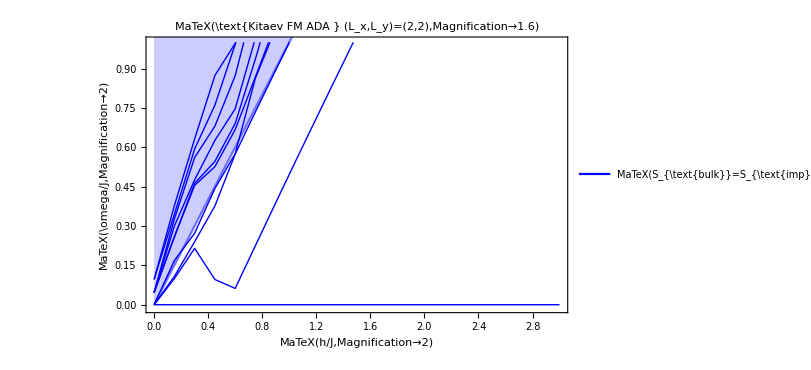

FigSpin

FigSpinOther

```mathematica
Begin["KitaevAda22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### (3,3) code spin 3/2 g=5

```mathematica
Begin["KitaevAda33S15`"]; 
$FileName="Kitaev-g5.m";

systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,1.2,1.2/40};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0, \\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"g0"->ToString[N@g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.13]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
(*, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]*)
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]] ];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]  ];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]   ];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_ADA_size=(3,3)_Simp=1.5\h=Range[0,1.2,0.03]_JK={0.5}_k=10.txt

$Aborted

KitaevAda33S15`

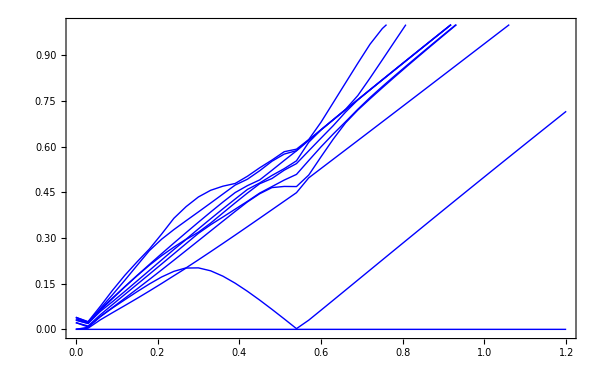

FigSpin

FigSpinOther

```mathematica
Begin["KitaevAda33S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### XXZ FM ADA (2,2)

#### code spin 1/2

```mathematica
Begin["Ada22S05`"]; 

$FileName="XXZ-h.m";
systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,1.5,.03};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 20; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{bulk}}=S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,1.5,0.03]_JK={0.5}_k=20.txt

$Aborted

Ada22S05`

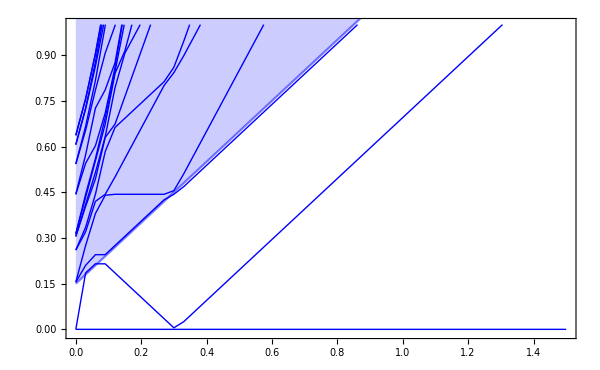

FigSpin

FigSpinOther

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code spin 1 bulk 1

```mathematica
Begin["Ada22S11`"]; 

$FileName="XXZ-h-1.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1};
impuritySpin     = {1};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.2};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;      Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

h Range length= 11

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-1.5\XXZ_FM_ADA_size=(2,2)_Simp=1.0\h=Range[0,2,0.2]_JK={0.5}_k=10.txt

$Aborted

Ada22S11`

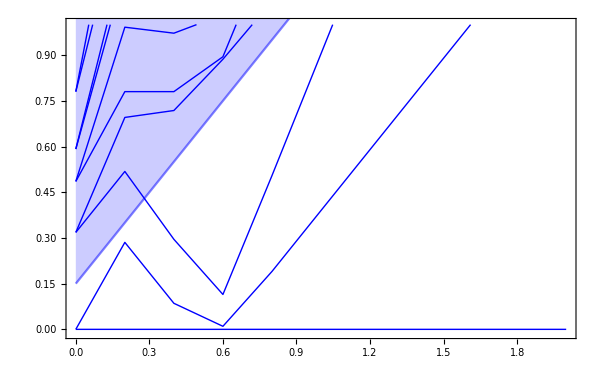

FigSpin

FigSpinOther

```mathematica
Begin["Ada22S11`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code s=simp=3/2

```mathematica
Begin["Ada22Sbulk15`"]; 
$FileName="XXZ-h-1.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {3/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.1};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 10; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;       
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;5]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,2}  ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

h Range length= 21

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-1.5\XXZ_FM_ADA_size=(2,2)_Simp=1.5\h=Range[0,2,0.1]_JK={0.5}_k=10.txt

$Aborted

Ada22Sbulk15`

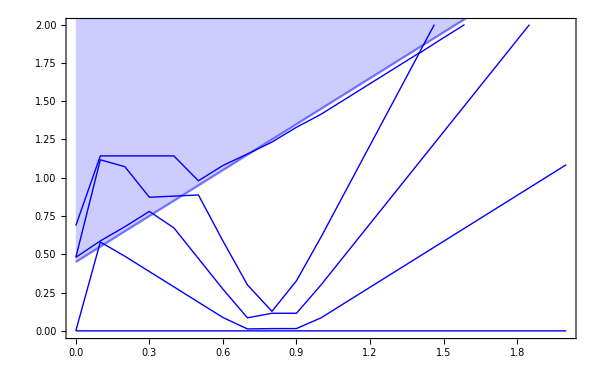

FigSpin

FigSpinOther

```mathematica
Begin["Ada22Sbulk15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code s=3/2 simp=1/2 (!!)

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;
 
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ](*
, Plot[  2Sbulk( 3/2 Norm[λn])+h+.001,{h,Min@hRange,Max@hRange},PlotStyle->{White}, Filling->Top,FillingStyle->Opacity[1]]*)
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Thick}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
]
End[]
```

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=50.txt

$Aborted

Ada22Sbulk15simp05`

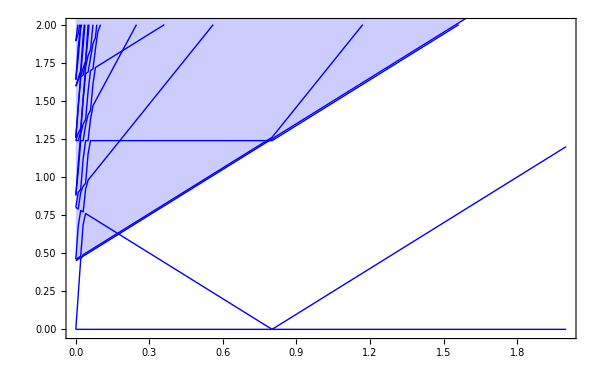

FigSpin

FigSpinOther

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### export

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S05"<>".pdf" }],   Ada22S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S05"<>".pdf"  }],  Ada22S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S1"<>".pdf"  }],  Ada22S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S1"<>".pdf"  }],  Ada22S1`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S15"<>".pdf" }],   Ada22S15`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S15"<>".pdf"  }],  Ada22S15`FigSpin ];
```

### XXZ FM ADA (3,3)

### Disp XXZ ADA LSW S=1/2 Simp=1/2 (! !)

```mathematica
JkValues[[1;;16]]
```

{0.05,0.0633333,0.0766667,0.09,0.103333,0.116667,0.13,0.143333,0.156667,0.17,0.183333,0.196667,0.21,0.223333,0.236667,0.25}

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=0.5_Si=0.5-ADA.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 30; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","LWS_data","data_XXZ_ada_S0.5.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=bulkSpin[[1]]  Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,.78},{-.01,.78}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> plotrange]  ;

figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->plotrange   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->plotrange] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->plotrange   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> plotrange ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{{-.01,.8},{-.01,.8}}      ]
End[]
```

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-ADA\XXZ_FM_ADA_size=(3,3)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=30.txt

-Graphics-

Ada22Sbulk15simp05`

### Disp XXZ ADA LSW S=3/2 Simp=1/2 (!!!)

```mathematica
JkValues[[1;;16]]
```

{0.05,0.0966667,0.143333,0.19,0.236667,0.283333,0.33,0.376667,0.423333,0.47,0.516667,0.563333,0.61,0.656667,0.703333,0.75}

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=50.txt

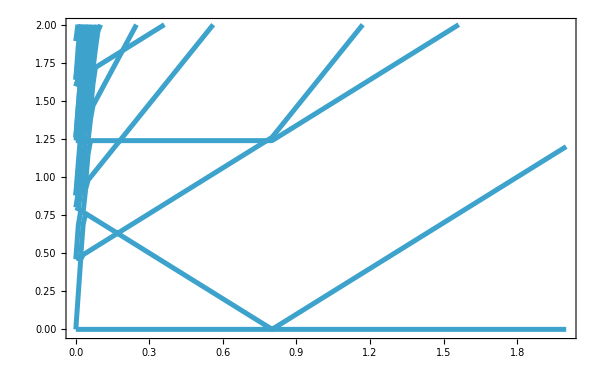
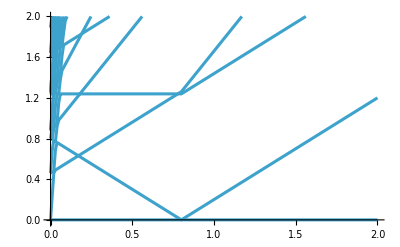
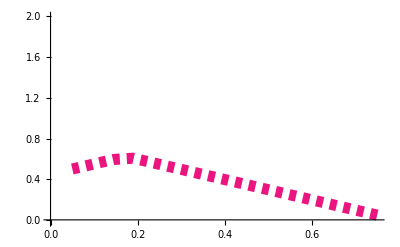
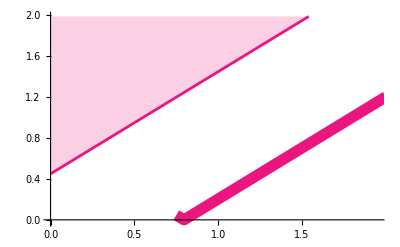

-Graphics-

Ada22Sbulk15simp05`

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","data_XXZ_ada.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=1.5 Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;(*
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	*)

	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]  ;

(*figDispLSWcont=Show[ListPlot[ Transpose[Thread/@JkDisp][[2;;-1]],PlotStyle->{{Magenta,Thickness[0.006],Opacity[0.95] }},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange->{ {0.75,2},{-.02,2}}   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Magenta,Thick}, Filling->Top,
PlotRange->{ {0,2},{-.02,2}}] ];*)
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->{ {0,1.95},{-.02,1.99}}   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->{ {0,2},{-.02,1.99}}] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->{ {0,0.75},{-.02,2}}   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> {-.02,2}  ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{ {0,2},{-.02,2.03}}]
End[]
```

```mathematica
(*Module[{plotLegend,g=1,JK=0.5,sb=1.5,si=.5},

	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@si ],"sb"->ToString[TeXForm@Rationalize@N@sb ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[0.1]
}] ;

ListPlot[Transpose[Thread/@JkDisp],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]
]*)
```

```mathematica
(*Number[StringReplace[dataLSW[[1,1]], "e"->"*^"]]*)
```

### Spin XXZ ADA LSW S=3/2 Simp=1/2 (!!!)

```mathematica
Begin["Ada22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","data_XXZ_ada.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=1.5 Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},

	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};

	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };


FigSpinED=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];

	plotTitle  = StringReplace[StringJoin[{"\\text{Adatom} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]  ;
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->{ {0,1.95},{-.02,1.99}}   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->{ {0,2},{-.02,1.99}}] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->{ {0,0.75},{-.02,2}}   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> {-.02,2}  ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{ {0,2},{-.02,2.03}}]
End[]
```

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_spin_components.txt

OpenRead::noopen: Cannot open C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_spin_components.txt.

Failed to OpenRead file at:

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_spin_components.txt

$Aborted

-Graphics--Graphics--Graphics--Graphics-

-Graphics-

Ada22Sbulk15simp05`

```mathematica
(*Module[{plotLegend,g=1,JK=0.5,sb=1.5,si=.5},

	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@si ],"sb"->ToString[TeXForm@Rationalize@N@sb ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[0.1]
}] ;

ListPlot[Transpose[Thread/@JkDisp],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]
]*)
```

```mathematica
(*Number[StringReplace[dataLSW[[1,1]], "e"->"*^"]]*)
```

## Figures - Substitution Case

```mathematica
plotRange={-.02,.4};
```

### Kitaev SUB

#### (2,2) code spin 3/2

```mathematica
Begin["KitaevSub22S15`"]; 
$FileName="Kitaev-g5.m";

systemDimensions = {{2,2}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs                             = {7};
KondoCoupling    = {.5010};
hRange           = {0,1,1./20};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0, \\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"g0"->ToString[N@g],"si"->ToString[N@impuritySpin],"jk"->ToString[ round[JK,100]  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_SUB_size=(2,2)_Simp=1.5\h=Range[0,1,0.05]_JK={0.501}_k=10.txt

$Aborted

KitaevSub22S15`

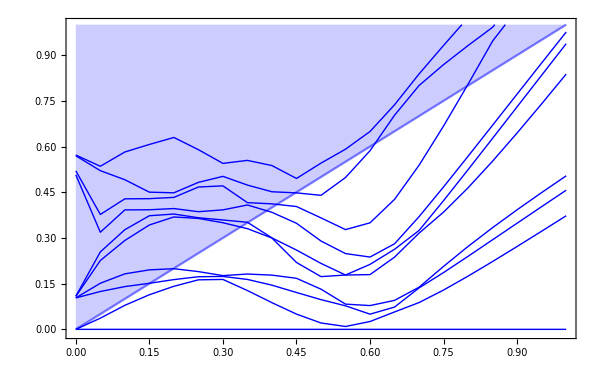

FigSpin

FigSpinOther

```mathematica
Begin["KitaevSub22S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### (3,3) code spin 3/2

```mathematica
Begin["KitaevSub33S15`"]; 
$FileName="Kitaev-g5.m";

systemDimensions = {{3,3}};
kitaev           = {{-1,-1,-1}};
heisenberg       = {0{1,1,1}};
anisotropy       = {0 cvec}; 
impuritySpin     = {3/2};
gs               = {5};
KondoCoupling    = {.5};
hRange           = {0,1.2,1.2/40};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 10; 
HamCoupling="Kitaev_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["g=g0, \\, S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk",
{"si"->ToString[N@impuritySpin],"g0"->ToString[N@g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.13]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
(*, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]*)
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]] ];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]  ];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]   ];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\Kitaev-g5\Kitaev_FM_SUB_size=(3,3)_Simp=1.5\h=Range[0,1.2,0.03]_JK={0.5}_k=10.txt

$Aborted

KitaevSub33S15`

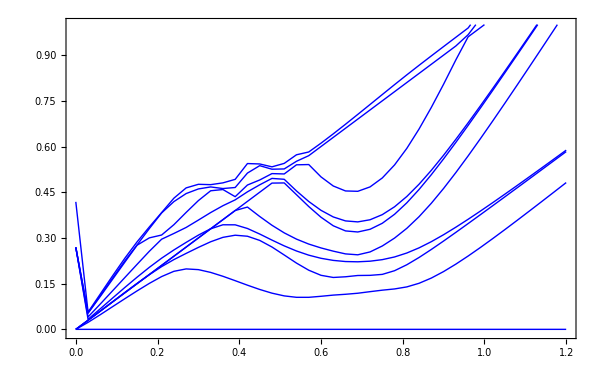

FigSpin

FigSpinOther

```mathematica
Begin["KitaevSub33S15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### XXZ FM SUB (2,2)

#### code spin 1/2

```mathematica
Begin["Sub22S05`"]; 

$FileName="XXZ-h.m";systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {0.57};
KondoCoupling    = {.5};
hRange           = {0,1.1,.03};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 120; 
HamCoupling="XXZ_FM_SUB";

dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;      Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["S_{\\text{imp}}=si, \\, J_{\\mathrm{K}}=jk , \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.3]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.01,1}  ]
, Plot[  3/2 Norm[λn]+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;
	figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL",
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];

]
End[]
```

h Range length= 37

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,1.1,0.03]_JK={0.5}_k=120.txt

$Aborted

Sub22S05`

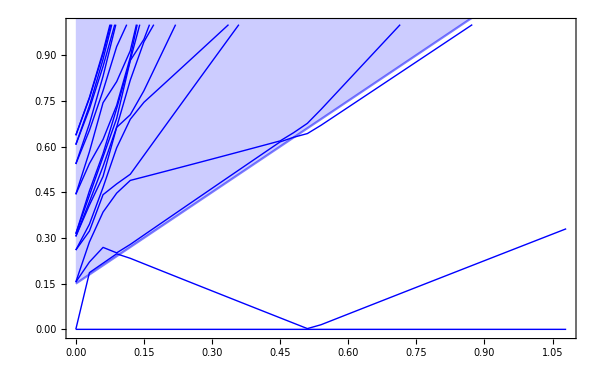

FigSpin

FigSpinOther

```mathematica
Begin["Sub22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

#### code s=simp=3/2

```mathematica
Begin["Sub22Sbulk15`"]; 
$FileName="XXZ-h-1.5.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {3/2};
gs               = {0.57};
KondoCoupling    = {.5};
hRange           = {0,8,.2};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 6; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;   
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;4]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,3}  ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h+.001,{h,Min@hRange,Max@hRange},PlotStyle->{White}, Filling->Top,FillingStyle->Opacity[1]]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Thick}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];


FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
]
End[]
```

h Range length= 41

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-1.5\XXZ_FM_SUB_size=(2,2)_Simp=1.5\h=Range[0,8,0.2]_JK={0.5}_k=6.txt

$Aborted

Sub22Sbulk15`

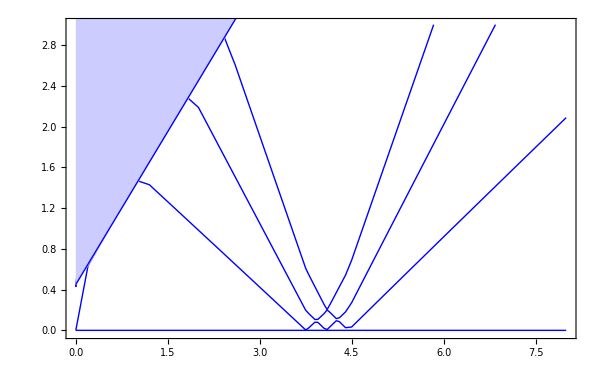

FigSpin

FigSpinOther

```mathematica
Begin["Sub22Sbulk15`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

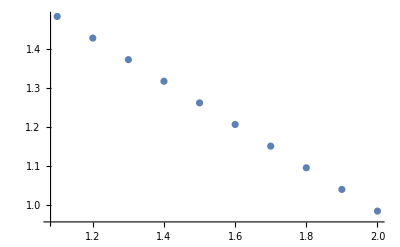

{a→-0.557073,b→3.76535}

```mathematica
Begin["Sub22Sbulk15`"]; 

ListPlot[ Transpose[Thread/@levels][[2]][[-10;;-1]] ]
 FindFit[   Transpose[Thread/@levels][[2]][[-10;;-1]]    ,  a (x-b), {{a,-.5},{b,4}},x]

End[];
```

```mathematica
a (x-b)/.{a->-0.5570734482159516,b->3.765349535481436}
```

-0.557073 (-3.76535+x)

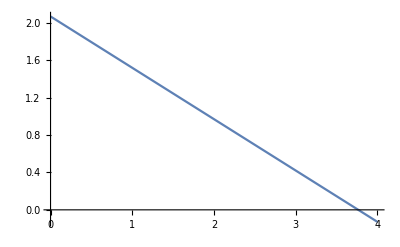

```mathematica
Plot[    -0.55 (-3.765349 +x)   ,{x,0,4}]
```

#### code s=3/2 simp=1/2 (!!)

```mathematica
Begin["Sub22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5-2.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,5,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40; 

HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;   
Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues},
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;klevels]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
	figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,3}  ]
(*, Plot[  2Sbulk( 3/2 Norm[λn])+h+.001,{h,Min@hRange,Max@hRange},PlotStyle->{White}, Filling->Top,FillingStyle->Opacity[1]]*)
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Blue,Thick}, Filling->Top]
] ;
	
figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.01,.18}} ] ;      ]


Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,Sbulk,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];

	{{Lx,Ly},K,J,λn,h,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];

FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
]
End[]
```

h Range length= 251

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5-2\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,5,0.02]_JK={0.5}_k=40.txt

$Aborted

Sub22Sbulk15simp05`

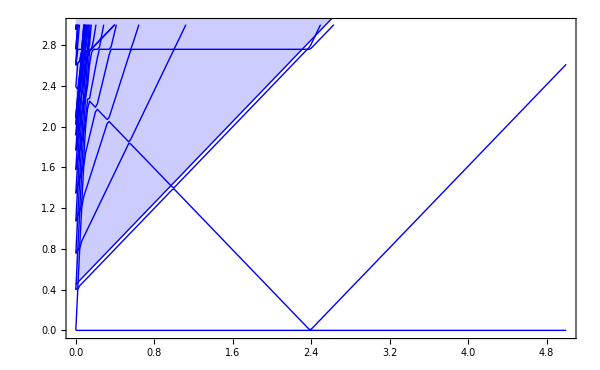

FigSpin

FigSpinOther

```mathematica
Begin["Sub22Sbulk15simp05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]     ]  *)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Sub22Sbulk15`"]; 

ListPlot[ Transpose[Thread/@levels][[2]][[-10;;-1]] ]
 FindFit[   Transpose[Thread/@levels][[2]][[-10;;-1]]    ,  a (x-b), {{a,-.5},{b,4}},x]

End[];
```

-Graphics-

{a→-0.557073,b→3.76535}

```mathematica
a (x-b)/.{a->-0.5570734482159516,b->3.765349535481436}
```

-0.557073 (-3.76535+x)

```mathematica
Plot[    -0.55 (-3.765349 +x)   ,{x,0,4}]
```

-Graphics-

#### export

```mathematica
Begin["Ada22S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Begin["Ada22S1`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

```mathematica
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S05"<>".pdf" }],   Ada22S05`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S05"<>".pdf"  }],  Ada22S05`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S1"<>".pdf"  }],  Ada22S1`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S1"<>".pdf"  }],  Ada22S1`FigSpin ];
Export[     FileNameJoin[{ figFolder,"FigEn"<>"Ada22S15"<>".pdf" }],   Ada22S15`figEn ];
Export[     FileNameJoin[{ figFolder,"FigSpin"<>"Ada22S15"<>".pdf"  }],  Ada22S15`FigSpin ];
```

### XXZ FM SUB (3,3)

#### code spin 1/2 (!!)

```mathematica
(*MaTeX["\\begin{array}{l} S_{\\text{bulk}}=S_{\\text{imp}}=si, \\\\[5pt] g=g0,\\,J_{\\mathrm{K}}=jk
\\end{array}",Magnification->2]*)
```

```mathematica
Begin["Sub33S05`"]; 
$FileName="XXZ-h.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,2./50};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs} ]; 
klevels          = 3; 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;        Print["h Range length= ",Length@hRange];

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,nl}, nl=klevels;
	{{Lx,Ly},K,J,λn,JK,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  dataRead[datapath];
ev=eValues;
	levels         = Transpose@{#[[;;,1]],(#[[;;,2,1;;nl]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace["\\begin{array}{l} S_{\\text{bulk}}=S_{\\text{imp}}=si, \\\\[5pt] g=g0,\\,J_{\\mathrm{K}}=jk
\\end{array}",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"g0"->ToString[Round@g],"jk"->ToString[ JK  ],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;		figEn=Show[ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.15]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->Hue[0.5,0,0.7,0.8],Background->Hue[0,0,1,0.8]]&)(*"Panel"*)],{Scaled[{.001,1}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {All,{-.01,1} } ]
, Plot[ (* 2Simp*) 3/2 Norm[λn]+  h,{h,Min@hRange,Max@hRange},PlotRange->{0,1},PlotStyle->{Blue,Opacity[.5]}, Filling->Top]
] ;figEnZoom=ListPlot[Transpose[Thread/@levels],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],  
(*FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/K","\\omega/K"},*)
ImageSize->600,PlotRange->{{0,.8},{-.02,.18}} ] ;      ]
Module[{Lx,Ly,J,λn,Simp,K,h,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour},
Abort[];
	{{Lx,Ly},K,J,λn,h,Simp,g}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	(*scriptName= StringReplace[HamCoupling,{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;;
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};*)
	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	data       =  Sort@dataRead[datapath]; 
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
	plotTitle  = (MaTeX[#,Magnification->1.6]&)@ StringReplace["J=-1, \\; S_{\\text{imp}}=si"(*, \\, \\mathbf{h}=h0 \\, \\mathbf{c}, \\, \\lambda=LL"*),
{"si"->ToString[N@impuritySpin],"h0"->ToString[Norm@hfields[[1]]],"LL"->ToString[-Norm@anisotropy[[1]]] }] ;
colour=CMYKColor[0.01,0.1,1,0.1];	
markers=opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],6},{Hue[Rational[347, 360], 0.4, 1],6},{colour,6} };
FigSpin=ListPlot[{ dataSimp[[3]] , dataS1[[3]] (*,  dataS2[[3]]*)   }, PlotRange->Full,
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{markers,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/h"," "},ImageSize->600,
PlotLegends->Placed[
LineLegend[ 
(MaTeX[#,Magnification->1.3]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{c}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{c}}\\rangle ",(*
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",*)
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{c}}\\rangle "        },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,.99,0.9]]&)(*"Panel"*)],
{Scaled[{.005,.005}],Scaled[{0,0}]}  ] 
];
FigSpinOther=ListPlot[{ dataSimp[[1]],dataSimp[[2]], dataS1[[1]], dataS1[[2]], dataS2[[1]] , dataS2[[2]]   },
PlotStyle->{Hue[Rational[197, 360], 0.7, 1],Hue[Rational[197, 360], 0.7, 1],Hue[Rational[347, 360], 0.4, 1],Hue[Rational[347, 360], 0.4, 1],colour,colour,colour },PlotMarkers-> Tuples@{ opensMarker/@{{Hue[Rational[197, 360], 0.7, 1],3},{Hue[Rational[197, 360], 0.7, 1],4},{Hue[Rational[347, 360], 0.4, 1],3},{Hue[Rational[347, 360], 0.4, 1],4},{colour,3},{colour,4} }  ,{Scaled[0.035]}},Joined->True,Frame->True,FrameStyle->Directive[Black,20,Thickness[.0035]],
PlotLabel->plotTitle,FrameLabel->(MaTeX[#,Magnification->2]&)/@{"J_K/|J|"," "},ImageSize->600,
PlotLegends->Placed[(MaTeX[#,Magnification->1]&)/@{
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{imp} }} \\cdot \\hat{\\mathbf{b}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{a}}\\rangle ",
"\\langle \\mathbf{S_{\\text{1} }} \\cdot \\hat{\\mathbf{b}}\\rangle ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{a}}\\rangle  ",
"\\langle \\mathbf{S_{\\text{2} }} \\cdot \\hat{\\mathbf{b}}\\rangle "        },
After (*{1.01,.5}*)]];
figEn
]
End[]
```

h Range length= 51

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h\XXZ_FM_SUB_size=(3,3)_Simp=0.5\h=Range[0,2,0.04]_JK={0.5}_k=3.txt

$Aborted

Sub33S05`

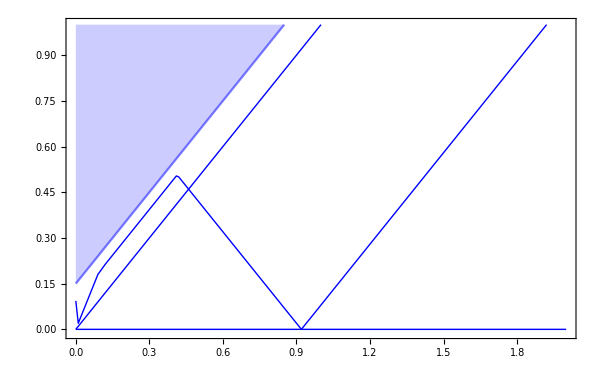

FigSpin

FigSpinOther

```mathematica
Begin["Sub33S05`"]; 
(*figEnInset=Show[figEn,Epilog-> Inset[figEnZoom,Scaled[{.98,.65}], Scaled[{1, 1}]  ,Scaled[.6] ]          ]*)
figEn
FigSpin
FigSpinOther
End[];
```

### Disp XXZ SUB LSW S=1/2 Simp=1/2 (! !)

```mathematica
Begin["Sub33bulk05simp05`"]; 
$FileName="XXZ-h-S=0.5_Si=0.5-SUB.m";

systemDimensions = {{3,3}}; 
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1.,1.,1.}};
anisotropy       = {-.1 cvec  }; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5001};
hRange           = {0,1.5,0.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40;
 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];

(*dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","LWS_data","data_XXZ_sub_S0.5.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];*)
JkValues = dataLSW[[1]];
EnValues=bulkSpin[[1]]  Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,1.5},{-.01,1.5}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S0.5_Si0.5_DISP.txt",Transpose[Thread/@levels] 
];	

 (*
plotTitle  = StringReplace[StringJoin[{"\\text{Substitution}  \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ round[ JK,100]  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> plotrange]  ;
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->plotrange   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->plotrange] 
];
figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->plotrange   ];
figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> plotrange ] ;*)
]
(*

Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{{-.01,1.51},{-.01,1.51}}       ]
End[]*)
```

h Range length= 151

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-SUB\XXZ_FM_SUB_size=(3,3)_Simp=0.5\h=Range[0,1.5,0.01]_JK={0.5001}_k=40.txt

### Disp XXZ SUB LSW S=1/2 Simp=1/2 ( teste )

h Range length= 75

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-SUB\XXZ_FM_SUB_size=(3,2)_Simp=0.5\h=Range[0.01,1.5,0.02]_JK={0.5}_k=40.txt

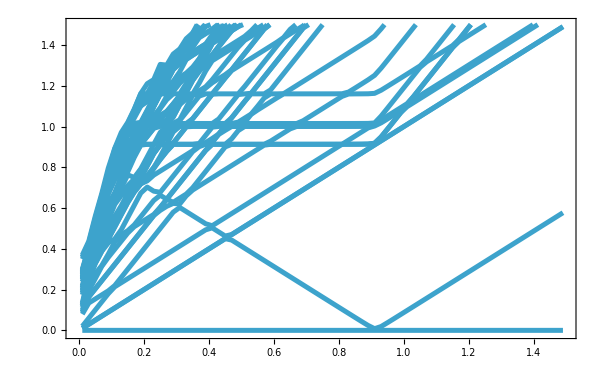
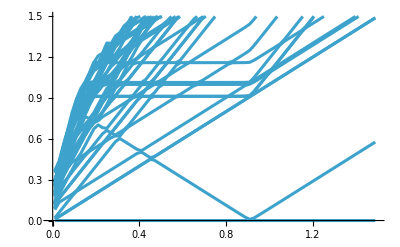
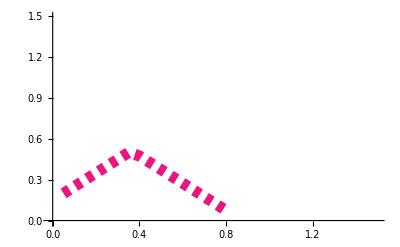
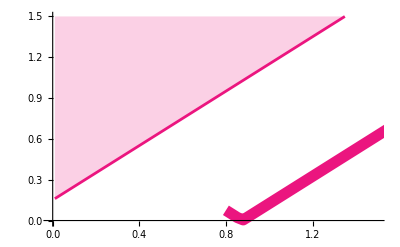

-Graphics-

Sub33bulk05simp05`

```mathematica
Begin["Sub33bulk05simp05`"]; 
$FileName="XXZ-h-S=0.5_Si=0.5-SUB.m";

systemDimensions = {{3,2}}; 
kitaev           = {0.01{-1,-1,-1}};
heisenberg       = {-{1.,1.001,1.}};
anisotropy       = {-.1 cvec +.01 avec  }; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0.01,1.5,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40;
 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","LWS_data","data_XXZ_sub_S0.5.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=bulkSpin[[1]]  Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,1.5},{-.01,1.5}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;
	plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\; (2,2) \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ round[ JK,100]  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	
figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> plotrange]  ;
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[16;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->plotrange   ]
, Plot[  2Sbulk( 3/2 Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->plotrange] 
];
figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;16]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->plotrange   ];
figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> plotrange ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{{-.01,1.51},{-.01,1.51}}       ]
End[]
```

### XXZ SUB LSW S=3/2 Simp=1/2 (!!)

```mathematica
JkValues[[1;;6]]
```

{0.05,0.2,0.35,0.5,0.65,0.8}

h Range length= 251

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_S=0.5-2\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,5,0.02]_JK={0.5}_k=40.txt

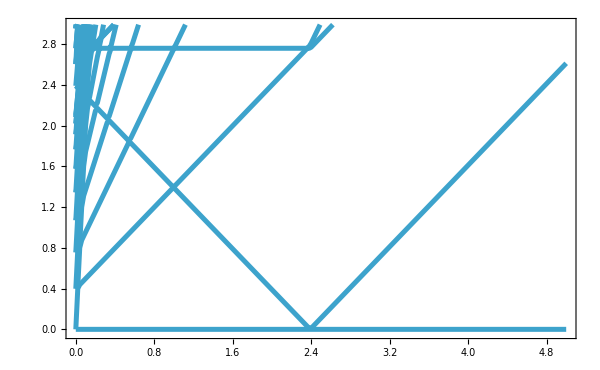
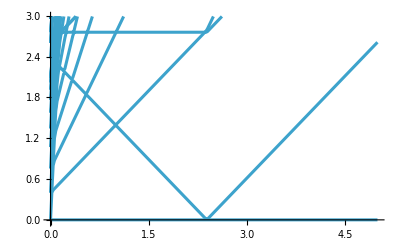
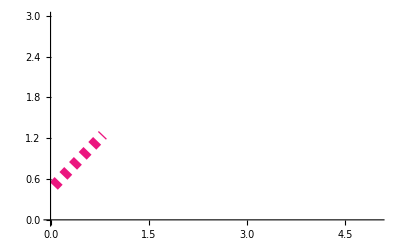
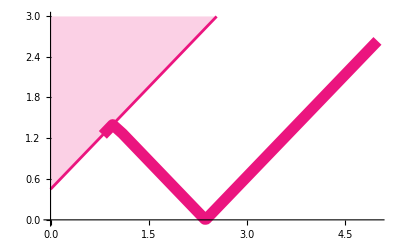

-Graphics-

Sub22Sbulk15simp05`

```mathematica
Begin["Sub22Sbulk15simp05`"]; 
$FileName="XXZ-h-S=1.5_S=0.5-2.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,5,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40; 

HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange;  
 
Print["h Range length= ",Length@hRange];

dataLSW=Module[{file,path,data},
path= FileNameJoin@{ NotebookDirectory[],"data","data_XXZ_sub.txt" };
file=OpenRead[path];
data=Interpreter["Number"]/@(StringSplit[ #,";"]&/@ReadList[file,Record,RecordSeparators->{"\n"} ]);
(*data= ReadList[file,Number,RecordLists->True];*)
Close[file];
data
];
JkValues = dataLSW[[1]];
EnValues=1.5 Transpose[  dataLSW[[2;;-1]]  ];
JkDisp =Thread@ {JkValues, EnValues  };



Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,prange={ {0,5},{-.03,2.99}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;(*
	plotTitle  = StringReplace[StringJoin["\\text{",StringReplace[HamCoupling,"_"->" "],"  } (L_x,L_y)=(LX,LY)"],{"LX"->ToString[systemDimensions[[1,1]]],"LY"->ToString[systemDimensions[[1,2]]]}] ;
	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	*)

	plotTitle  = StringReplace[StringJoin[{"\\text{Substitution} \\quad  S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk "}],
{"si"->ToString[TeXForm@Rationalize@N@impuritySpin[[1]] ],"sb"->ToString[TeXForm@Rationalize@N@Sbulk ],
"jk"->ToString[ JK  ],"g0"->ToString[Round@g],"LL"->ToString[-Norm@anisotropy[[1]]]
}] ;	

figDispED0=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.006] ,Opacity[1]}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]],PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{ED}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> prange    ]  ;

(*figDispLSWcont=Show[ListPlot[ Transpose[Thread/@JkDisp][[2;;-1]],PlotStyle->{{Magenta,Thickness[0.006],Opacity[0.95] }},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLabel->(MaTeX[#,Magnification->1.6]&)@plotTitle, PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange->{ {0.75,2},{-.02,2}}   ]
, Plot[  2Sbulk( (3/2) Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{Magenta,Thick}, Filling->Top,
PlotRange->{ {0,2},{-.02,2}}] ];*)
figDispLSWbs=Show[
ListPlot[  Transpose[Thread/@JkDisp[[6;;-1]] ][[1]] ,PlotStyle->{{color2,Thickness[0.02],Opacity[1] }},Joined->True,PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.5]&)@"\\text{LSW}" },LegendMarkers->Automatic],{Scaled[{.981,.98}], Scaled[{1, 1}]}],
PlotRange->prange]
, Plot[  2Sbulk( (3/2) Norm[λn])+h,{h,Min@hRange,Max@hRange},PlotStyle->{color2,Thickness[0.005]}, Filling->Top,
PlotRange->prange   ] 
];

figDispLSWbsDash=ListPlot[Transpose[Thread/@JkDisp[[1;;6]]][[1]],PlotStyle->{{color2,Dashed,Thickness[0.02],Opacity[1] }},Joined->True,
PlotRange->prange   ];

figDispED=ListPlot[Transpose[Thread/@levels],PlotStyle->{{color1,Thickness[0.0055] ,Opacity[1]}},Joined->True,
PlotRange-> prange   ] ;
]


Print[figDispED0,figDispED, figDispLSWbsDash,figDispLSWbs]

figDisp=Show[figDispED0, figDispLSWbsDash,figDispLSWbs,figDispED,
PlotRange->{ {0,4.8},{-.03,3.02}}    ]
End[]
```

```mathematica
(*Module[{plotLegend,g=1,JK=0.5,sb=1.5,si=.5},

	plotLegend= StringReplace[" S_{\\text{bulk}}= sb,\\, S_{\\text{imp}}=si, \\,  g=g0, \\, J_{\\mathrm{K}}=jk ",
{"si"->ToString[TeXForm@Rationalize@N@si ],"sb"->ToString[TeXForm@Rationalize@N@sb ],
"jk"->ToString[ JK  ],"g0"->ToString[ g],"LL"->ToString[0.1]
}] ;

ListPlot[Transpose[Thread/@JkDisp],PlotStyle->{{Blue,Thick}},Joined->True,Frame->True,FrameStyle->Directive[Black,18,Thickness[.002]], PlotLegends->Placed[LineLegend[{(MaTeX[#,Magnification->1.1]&)@plotLegend },LegendMarkers->Automatic,LegendFunction->(Framed[#,RoundingRadius->4,FrameStyle->LightGray,Background->Hue[0,0,1,0.9]]&)(*"Panel"*)],{Scaled[{.021,.98}], Scaled[{0, 1}]}],
FrameLabel->(MaTeX[#,Magnification->2]&)/@{"h/J","\\omega/J"},ImageSize->600,
PlotRange-> {-.02,2}  ]
]*)
```

```mathematica
(*Number[StringReplace[dataLSW[[1,1]], "e"->"*^"]]*)
```

## Spin (!!!)

### Spin XXZ ADA S=3/2 Simp=1/2

```mathematica
$FileName="XXZ-h-S=1.5_Si=0.5=ADA.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin          = {3/2};
impuritySpin     = {1/2};
gs                        = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 1; 
HamCoupling="XXZ_FM_ADA";

dataName=Module[{i,f,δ,k,jk}, 	
{i,f,δ}=hRange;  k=klevels;    
jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
	StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour,Sbulk},

{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
{Lx,Ly}=Round@{Lx,Ly}; 

 scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	

	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];

	Print[datapath];

	data       =  dataRead[datapath]; 

dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
data1=Table[ {hRange[[hi]], dataSimp[[3,hi,2]] },{hi,1,Length@hRange}];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
data2=Table[ {hRange[[hi]], dataS1[[3,hi,2]] },{hi,1,Length@hRange}];
(*
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
*)

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-ADA_S1.5_Si0.5_SPIN_IMP.txt",data1];
dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-ADA_S1.5_Si0.5_SPIN_BULK.txt",data2];


     ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_Si=0.5=ADA\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_spin_components.txt

### Spin XXZ ADA S=1/2 Simp=1/2

```mathematica
$FileName="XXZ-h-S=0.5_Si=0.5-ADA.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin          = {1/2};
impuritySpin     = {1/2};
gs                        = {1};
KondoCoupling    = {.5};
hRange           = {0,2,0.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 1; 
HamCoupling="XXZ_FM_ADA";

dataName=Module[{i,f,δ,k,jk}, 	
{i,f,δ}=hRange;  k=klevels;    
jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
	StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour,Sbulk},

{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
{Lx,Ly}=Round@{Lx,Ly}; 

 scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	

	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];

	Print[datapath];

	data       =  dataRead[datapath]; 

dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
data1=Table[ {hRange[[hi]], dataSimp[[3,hi,2]] },{hi,1,Length@hRange}];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
data2=Table[ {hRange[[hi]], dataS1[[3,hi,2]] },{hi,1,Length@hRange}];
(*
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
*)

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-ADA_S0.5_Si0.5_SPIN_IMP.txt",data1];
dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-ADA_S0.5_Si0.5_SPIN_BULK.txt",data2];

     ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-ADA\XXZ_FM_ADA_size=(3,3)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_spin_components.txt

### Spin XXZ SUB S=3/2 Simp=1/2

```mathematica
$FileName="XXZ-h-S=1.5_Si=0.5=SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin          = {3/2};
impuritySpin     = {1/2};
gs                        = {1};
KondoCoupling    = {.5};
hRange           = {0,4.2,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 1; 
HamCoupling="XXZ_FM_SUB";

dataName=Module[{i,f,δ,k,jk}, 	
{i,f,δ}=hRange;  k=klevels;    
jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
	StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour,Sbulk},

{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
{Lx,Ly}=Round@{Lx,Ly}; 

 scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	

	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];

	Print[datapath];

	data       =  dataRead[datapath]; 

dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
data1=Table[ {hRange[[hi]], dataSimp[[3,hi,2]] },{hi,1,Length@hRange}];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
data2=Table[ {hRange[[hi]], dataS1[[3,hi,2]] },{hi,1,Length@hRange}];
(*
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
*)

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S1.5_Si0.5_SPIN_IMP.txt",data1];
dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S1.5_Si0.5_SPIN_BULK.txt",data2];

     ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_Si=0.5=SUB\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,4.2,0.02]_JK={0.5}_spin_components.txt

### Spin XXZ SUB S=1/2 Simp=1/2

```mathematica
$FileName="XXZ-h-S=0.5_Si=0.5-SUB.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin          = {1/2};
impuritySpin     = {1/2};
gs                        = {1};
KondoCoupling    = {.5};
hRange           = {0,5,0.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 1; 
HamCoupling="XXZ_FM_SUB";

dataName=Module[{i,f,δ,k,jk}, 	
{i,f,δ}=hRange;  k=klevels;    
jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
	StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,data,dataSimp,dataS1,dataS2,colour,Sbulk},

{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	
{Lx,Ly}=Round@{Lx,Ly}; 

 scriptName= FileBaseName[$FileName]; 	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	

	datapath=dataPathTXT[StringJoin[dataName2,"_spin_components"],HamCoupling,Simp,{Lx,Ly},dataFolder];

	Print[datapath];

	data       =  dataRead[datapath]; 

dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
data1=Table[ {hRange[[hi]], dataSimp[[3,hi,2]] },{hi,1,Length@hRange}];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
data2=Table[ {hRange[[hi]], dataS1[[3,hi,2]] },{hi,1,Length@hRange}];
(*
	dataSimp=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,2}]]];
	dataS1=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,3}]]];
	dataS2=Chop[#,10^-7]&@Transpose[Thread/@data[[;;,{1,4}]]];
*)

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S0.5_Si0.5_SPIN_IMP.txt",data1];
dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S0.5_Si0.5_SPIN_BULK.txt",data2];

     ]
```

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-SUB\XXZ_FM_SUB_size=(3,3)_Simp=0.5\h=Range[0,5,0.02]_JK={0.5}_spin_components.txt

```mathematica
data1
```

{{0.,0.0508496},{0.04,0.0508496},{0.08,-0.358481},{0.12,-0.358481},{0.16,-0.358481},{0.2,-0.358481},{0.24,-0.358481},{0.28,-0.358481},{0.32,-0.358481},{0.36,-0.358481},{0.4,-0.358481},{0.44,-0.358481},{0.48,-0.358481},{0.52,-0.358481},{0.56,-0.358481},{0.6,-0.358481},{0.64,-0.358481},{0.68,-0.358481},{0.72,-0.358481},{0.76,-0.358481},{0.8,-0.358481},{0.84,-0.358481},{0.88,-0.358481},{0.92,-0.358481},{0.96,-0.358481},{1.,-0.358481},{1.04,-0.358481},{1.08,-0.358481},{1.12,-0.358481},{1.16,-0.358481},{1.2,-0.358481},{1.24,-0.358481},{1.28,-0.358481},{1.32,-0.358481},{1.36,-0.358481},{1.4,-0.358481},{1.44,-0.358481},{1.48,-0.358481},{1.52,-0.358481},{1.56,-0.358481},{1.6,-0.358481},{1.64,-0.358481},{1.68,-0.358481},{1.72,-0.358481},{1.76,-0.358481},{1.8,-0.358481},{1.84,-0.358481},{1.88,-0.358481},{1.92,0.5},{1.96,0.5},{2.,0.5},{2.04,0.5},{2.08,0.5},{2.12,0.5},{2.16,0.5},{2.2,0.5},{2.24,0.5},{2.28,0.5},{2.32,0.5},{2.36,0.5},{2.4,0.5},{2.44,0.5},{2.48,0.5},{2.52,0.5},{2.56,0.5},{2.6,0.5},{2.64,0.5},{2.68,0.5},{2.72,0.5},{2.76,0.5},{2.8,0.5},{2.84,0.5},{2.88,0.5},{2.92,0.5},{2.96,0.5},{3.,0.5},{3.04,0.5},{3.08,0.5},{3.12,0.5},{3.16,0.5},{3.2,0.5},{3.24,0.5},{3.28,0.5},{3.32,0.5},{3.36,0.5},{3.4,0.5},{3.44,0.5},{3.48,0.5},{3.52,0.5},{3.56,0.5},{3.6,0.5},{3.64,0.5},{3.68,0.5},{3.72,0.5},{3.76,0.5},{3.8,0.5},{3.84,0.5},{3.88,0.5},{3.92,0.5},{3.96,0.5},{4.,0.5},{4.04,0.5},{4.08,0.5},{4.12,0.5},{4.16,0.5},{4.2,0.5},{4.24,0.5},{4.28,0.5},{4.32,0.5},{4.36,0.5},{4.4,0.5},{4.44,0.5},{4.48,0.5},{4.52,0.5},{4.56,0.5},{4.6,0.5},{4.64,0.5},{4.68,0.5},{4.72,0.5},{4.76,0.5},{4.8,0.5},{4.84,0.5},{4.88,0.5},{4.92,0.5},{4.96,0.5},{5.,0.5},{5.04,0.5},{5.08,0.5},{5.12,0.5},{5.16,0.5},{5.2,0.5},{5.24,0.5},{5.28,0.5},{5.32,0.5},{5.36,0.5},{5.4,0.5},{5.44,0.5},{5.48,0.5},{5.52,0.5},{5.56,0.5},{5.6,0.5},{5.64,0.5},{5.68,0.5},{5.72,0.5},{5.76,0.5},{5.8,0.5},{5.84,0.5},{5.88,0.5},{5.92,0.5},{5.96,0.5},{6.,0.5},{6.04,0.5},{6.08,0.5},{6.12,0.5},{6.16,0.5},{6.2,0.5},{6.24,0.5},{6.28,0.5},{6.32,0.5},{6.36,0.5},{6.4,0.5},{6.44,0.5},{6.48,0.5},{6.52,0.5},{6.56,0.5},{6.6,0.5},{6.64,0.5},{6.68,0.5},{6.72,0.5},{6.76,0.5},{6.8,0.5},{6.84,0.5},{6.88,0.5},{6.92,0.5},{6.96,0.5},{7.,0.5},{7.04,0.5},{7.08,0.5},{7.12,0.5},{7.16,0.5},{7.2,0.5},{7.24,0.5},{7.28,0.5},{7.32,0.5},{7.36,0.5},{7.4,0.5},{7.44,0.5},{7.48,0.5},{7.52,0.5},{7.56,0.5},{7.6,0.5},{7.64,0.5},{7.68,0.5},{7.72,0.5},{7.76,0.5},{7.8,0.5},{7.84,0.5},{7.88,0.5},{7.92,0.5},{7.96,0.5},{8.,0.5},{8.04,0.5},{8.08,0.5},{8.12,0.5},{8.16,0.5},{8.2,0.5},{8.24,0.5},{8.28,0.5},{8.32,0.5},{8.36,0.5},{8.4,0.5},{8.44,0.5},{8.48,0.5},{8.52,0.5},{8.56,0.5},{8.6,0.5},{8.64,0.5},{8.68,0.5},{8.72,0.5},{8.76,0.5},{8.8,0.5},{8.84,0.5},{8.88,0.5},{8.92,0.5},{8.96,0.5},{9.,0.5},{9.04,0.5},{9.08,0.5},{9.12,0.5},{9.16,0.5},{9.2,0.5},{9.24,0.5},{9.28,0.5},{9.32,0.5},{9.36,0.5},{9.4,0.5},{9.44,0.5},{9.48,0.5},{9.52,0.5},{9.56,0.5},{9.6,0.5},{9.64,0.5},{9.68,0.5},{9.72,0.5},{9.76,0.5},{9.8,0.5},{9.84,0.5},{9.88,0.5},{9.92,0.5},{9.96,0.5},{10.,0.5}}

```mathematica
data2
```

{{0.,-0.0646759},{0.04,-0.0646759},{0.08,0.455953},{0.12,0.455953},{0.16,0.455953},{0.2,0.455953},{0.24,0.455953},{0.28,0.455953},{0.32,0.455953},{0.36,0.455953},{0.4,0.455953},{0.44,0.455953},{0.48,0.455953},{0.52,0.455953},{0.56,0.455953},{0.6,0.455953},{0.64,0.455953},{0.68,0.455953},{0.72,0.455953},{0.76,0.455953},{0.8,0.455953},{0.84,0.455953},{0.88,0.455953},{0.92,0.455953},{0.96,0.455953},{1.,0.455953},{1.04,0.455953},{1.08,0.455953},{1.12,0.455953},{1.16,0.455953},{1.2,0.455953},{1.24,0.455953},{1.28,0.455953},{1.32,0.455953},{1.36,0.455953},{1.4,0.455953},{1.44,0.455953},{1.48,0.455953},{1.52,0.455953},{1.56,0.455953},{1.6,0.455953},{1.64,0.455953},{1.68,0.455953},{1.72,0.455953},{1.76,0.455953},{1.8,0.455953},{1.84,0.455953},{1.88,0.455953},{1.92,0.5},{1.96,0.5},{2.,0.5},{2.04,0.5},{2.08,0.5},{2.12,0.5},{2.16,0.5},{2.2,0.5},{2.24,0.5},{2.28,0.5},{2.32,0.5},{2.36,0.5},{2.4,0.5},{2.44,0.5},{2.48,0.5},{2.52,0.5},{2.56,0.5},{2.6,0.5},{2.64,0.5},{2.68,0.5},{2.72,0.5},{2.76,0.5},{2.8,0.5},{2.84,0.5},{2.88,0.5},{2.92,0.5},{2.96,0.5},{3.,0.5},{3.04,0.5},{3.08,0.5},{3.12,0.5},{3.16,0.5},{3.2,0.5},{3.24,0.5},{3.28,0.5},{3.32,0.5},{3.36,0.5},{3.4,0.5},{3.44,0.5},{3.48,0.5},{3.52,0.5},{3.56,0.5},{3.6,0.5},{3.64,0.5},{3.68,0.5},{3.72,0.5},{3.76,0.5},{3.8,0.5},{3.84,0.5},{3.88,0.5},{3.92,0.5},{3.96,0.5},{4.,0.5},{4.04,0.5},{4.08,0.5},{4.12,0.5},{4.16,0.5},{4.2,0.5},{4.24,0.5},{4.28,0.5},{4.32,0.5},{4.36,0.5},{4.4,0.5},{4.44,0.5},{4.48,0.5},{4.52,0.5},{4.56,0.5},{4.6,0.5},{4.64,0.5},{4.68,0.5},{4.72,0.5},{4.76,0.5},{4.8,0.5},{4.84,0.5},{4.88,0.5},{4.92,0.5},{4.96,0.5},{5.,0.5},{5.04,0.5},{5.08,0.5},{5.12,0.5},{5.16,0.5},{5.2,0.5},{5.24,0.5},{5.28,0.5},{5.32,0.5},{5.36,0.5},{5.4,0.5},{5.44,0.5},{5.48,0.5},{5.52,0.5},{5.56,0.5},{5.6,0.5},{5.64,0.5},{5.68,0.5},{5.72,0.5},{5.76,0.5},{5.8,0.5},{5.84,0.5},{5.88,0.5},{5.92,0.5},{5.96,0.5},{6.,0.5},{6.04,0.5},{6.08,0.5},{6.12,0.5},{6.16,0.5},{6.2,0.5},{6.24,0.5},{6.28,0.5},{6.32,0.5},{6.36,0.5},{6.4,0.5},{6.44,0.5},{6.48,0.5},{6.52,0.5},{6.56,0.5},{6.6,0.5},{6.64,0.5},{6.68,0.5},{6.72,0.5},{6.76,0.5},{6.8,0.5},{6.84,0.5},{6.88,0.5},{6.92,0.5},{6.96,0.5},{7.,0.5},{7.04,0.5},{7.08,0.5},{7.12,0.5},{7.16,0.5},{7.2,0.5},{7.24,0.5},{7.28,0.5},{7.32,0.5},{7.36,0.5},{7.4,0.5},{7.44,0.5},{7.48,0.5},{7.52,0.5},{7.56,0.5},{7.6,0.5},{7.64,0.5},{7.68,0.5},{7.72,0.5},{7.76,0.5},{7.8,0.5},{7.84,0.5},{7.88,0.5},{7.92,0.5},{7.96,0.5},{8.,0.5},{8.04,0.5},{8.08,0.5},{8.12,0.5},{8.16,0.5},{8.2,0.5},{8.24,0.5},{8.28,0.5},{8.32,0.5},{8.36,0.5},{8.4,0.5},{8.44,0.5},{8.48,0.5},{8.52,0.5},{8.56,0.5},{8.6,0.5},{8.64,0.5},{8.68,0.5},{8.72,0.5},{8.76,0.5},{8.8,0.5},{8.84,0.5},{8.88,0.5},{8.92,0.5},{8.96,0.5},{9.,0.5},{9.04,0.5},{9.08,0.5},{9.12,0.5},{9.16,0.5},{9.2,0.5},{9.24,0.5},{9.28,0.5},{9.32,0.5},{9.36,0.5},{9.4,0.5},{9.44,0.5},{9.48,0.5},{9.52,0.5},{9.56,0.5},{9.6,0.5},{9.64,0.5},{9.68,0.5},{9.72,0.5},{9.76,0.5},{9.8,0.5},{9.84,0.5},{9.88,0.5},{9.92,0.5},{9.96,0.5},{10.,0.5}}

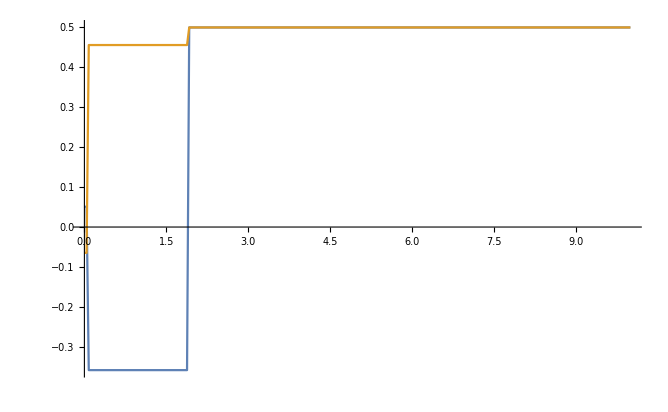

```mathematica
ListPlot[ {data1,data2},PlotRange->Full,Joined->True]
```

## Disp

### Disp XXZ SUB S=1/2 Simp=1/2

```mathematica
Begin["Sub33bulk05simp05`"]; 
$FileName="XXZ-h-S=0.5_Si=0.5-SUB.m";

systemDimensions = {{3,3}}; 
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1.,1.,1.}};
anisotropy       = {-.1 cvec  }; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5001};
hRange           = {0,1.5,0.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40;
 
HamCoupling="XXZ_FM_SUB";
dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,1.5},{-.01,1.5}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S0.5_Si0.5_DISP.txt",Transpose[Thread/@levels] 
];	
]
```

h Range length= 151

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-SUB\XXZ_FM_SUB_size=(3,3)_Simp=0.5\h=Range[0,1.5,0.01]_JK={0.5001}_k=40.txt

### Disp XXZ SUB S=3/2 Simp=1/2

h Range length= 251

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_Si=0.5=SUB\XXZ_FM_SUB_size=(2,2)_Simp=0.5\h=Range[0,5,0.02]_JK={0.5}_k=40.txt

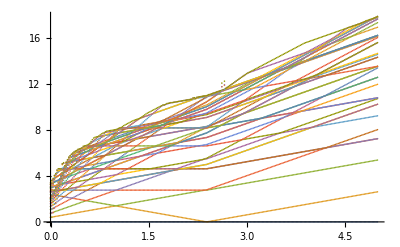

```mathematica
$FileName="XXZ-h-S=1.5_Si=0.5=SUB.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,5,.02};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 40; 
HamCoupling="XXZ_FM_SUB";

dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,1.5},{-.01,1.5}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;

Print[  ListPlot[Transpose[Thread/@levels] ]   ];

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\XXZ-SUB_S1.5_Si0.5_DISP.txt",Transpose[Thread/@levels] 
];	

]
```

### Disp XXZ ADA S=1/2 Simp=1/2

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=0.5_Si=0.5-ADA\XXZ_FM_ADA_size=(3,3)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=30.txt

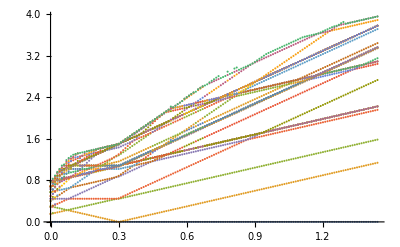

```mathematica
$FileName="XXZ-h-S=0.5_Si=0.5-ADA.m";

systemDimensions = {{3,3}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {1/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 30; 
HamCoupling="XXZ_FM_ADA";

dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,1.5},{-.01,1.5}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;

Print[  ListPlot[Transpose[Thread/@levels] ]   ];

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\ED\\XXZ-ADA_S0.5_Si0.5_DISP.txt",Transpose[Thread/@levels] 
];	

]
```

### Disp XXZ ADA S=3/2 Simp=1/2

h Range length= 201

C:\User\lucas\Desktop\Wolfram Mathematica\PhD-codes\ED-QM-Impurity\data\XXZ-h-S=1.5_Si=0.5=ADA\XXZ_FM_ADA_size=(2,2)_Simp=0.5\h=Range[0,2,0.01]_JK={0.5}_k=50.txt

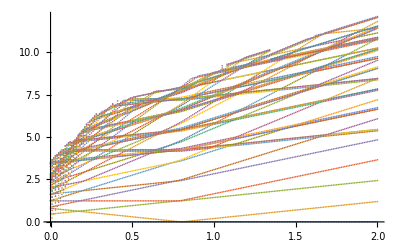

```mathematica
$FileName="XXZ-h-S=1.5_Si=0.5=ADA.m";

systemDimensions = {{2,2}};
kitaev           = {0{-1,-1,-1}};
heisenberg       = {-{1,1,1}};
anisotropy       = {-.1 cvec}; 
bulkSpin         = {3/2};
impuritySpin     = {1/2};
gs               = {1};
KondoCoupling    = {.5};
hRange           = {0,2,.01};
parameters       = N@Tuples[{systemDimensions,kitaev,heisenberg,anisotropy,KondoCoupling,impuritySpin,gs,bulkSpin} ]; 
klevels          = 50; 
HamCoupling="XXZ_FM_ADA";

dataName=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;    jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};					
StringReplace["h=Range[i,f,d]_JK=jk_k=k0", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];
dataName2=Module[{i,f,δ,k,jk}, 	{i,f,δ}=hRange;  k=klevels;  jk=KondoCoupling;  {i,f,δ,k,jk}=ToString/@{i,f,δ,k,jk};				
StringReplace["h=Range[i,f,d]_JK=jk", {"i"->i,"f"->f,"d"->δ,"k0"->k,"jk"->jk}]  ];

hRange=Range@@hRange; 

Print["h Range length= ",Length@hRange];


Module[{Lx,Ly,J,λn,Simp,K,JK,g,H0,HJ,HI,HK,HZ,path,datapath,plotTitle,plotLegend,dataFolder,scriptName,eValues,color1=cyan,color2=pink,
plotrange={{-.01,1.5},{-.01,1.5}}   },
	{{Lx,Ly},K,J,λn,JK,Simp,g,Sbulk}=parameters[[1]]; 	{Lx,Ly}=Round@{Lx,Ly};  scriptName= FileBaseName[$FileName];
	dataFolder= FileNameJoin@{Directory[],"data",scriptName};
	datapath     =  dataPathTXT[dataName,HamCoupling,Simp,{Lx,Ly},dataFolder];
	Print[datapath];
	eValues      =  Sort@dataRead[datapath];
	levels         = Transpose@{#[[;;,1]],(#[[;;,2]]-#[[;;,2,1]])}&@eValues;

Print[  ListPlot[Transpose[Thread/@levels] ]   ];

dataWrite["C:\\User\\lucas\\Desktop\\Wolfram Mathematica\\PhD-codes\\ED-QM-Impurity\\data\\ED\\XXZ-ADA_S1.5_Si0.5_DISP.txt",Transpose[Thread/@levels] 
];	

]
```

```mathematica
file=OpenRead[path];
data=ReadList[file];
Close[file];
```